```mathematica
log = FullSimplify[Laplacian[(1/(2*Pi*σ^2))*Exp[-(x^2+y^2)/(2*σ^2)],{x,y}]]
FullSimplify[log==(-1/(Pi*σ^4))*(1-((x^2+y^2)/(2*σ^2)))*Exp[-(x^2+y^2)/(2*σ^2)]]
FullSimplify[log==(1/(2*Pi*σ^2))*((x^2+y^2-2*σ^2)/(σ^4))*Exp[-(x^2+y^2)/(2*σ^2)]]
```

(ⅇ^(-(x^2+y^2)/(2 σ^2)) (x^2+y^2-2 σ^2))/(2 π σ^6)

True

True

```mathematica
g  =(1/(2*Pi*σ^2))*Exp[-(x^2+y^2)/(2*σ^2)];
xx = FullSimplify[D[g, {x, 2}]]
yy =   FullSimplify[D[g, {y, 2}]]
logg = xx + yy;
FullSimplify[logg == log]
FullSimplify[(1/(2*Pi*σ^2))*xx +(1/(2*Pi*σ^2))* yy==log]
FullSimplify[(1/(2*Pi*σ^2))*((x^2-σ^2)/σ^4)*Exp[-(x^2+y^2)/(2*σ^2)] +(1/(2*Pi*σ^2))* ((y^2-σ^2)/σ^4)*Exp[-(x^2+y^2)/(2*σ^2)]==log]
```

(ⅇ^(-(x^2+y^2)/(2 σ^2)) (x-σ) (x+σ))/(2 π σ^6)

(ⅇ^(-(x^2+y^2)/(2 σ^2)) (y-σ) (y+σ))/(2 π σ^6)

True

(ⅇ^(-(x^2+y^2)/(2 σ^2)) (x^2+y^2-2 σ^2) (-1+2 π σ^2))/σ==0

True

(1 | 1
2 | 1
2 | 2
1 | 2)

(2 | 2
3 | 2
3 | 3
2 | 3)

{0.,TransformationFunction[(1. | 0. | 1.
0. | 1. | 1.
0. | 0. | 1.)]}

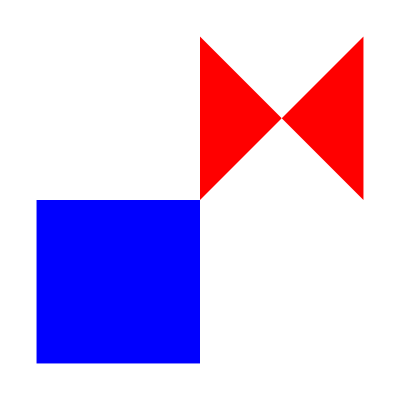

```mathematica
(* Question 4.1 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp ={{2,2},{3,2},{3,3},{2,3}};
MatrixForm[x]
MatrixForm[xp]
{error, f} = FindGeometricTransform[xp, x]
(*MatrixForm[f[x]]*)
Graphics[{{Blue,Polygon[x]},{Red, f[Polygon[x]]}}]
```

(1 | 1
2 | 1
2 | 2
1 | 2)

(0 | √2
-1/(√2)+√2 | 1/(√2)+√2
0 | 2 √2
1/(√2)-√2 | 1/(√2)+√2)

{3.24968×10^-16,TransformationFunction[(0.707107 | -0.707107 | 2.22045×10^-16
0.707107 | 0.707107 | 0.
0. | 0. | 1.)]}

(1.11022×10^-16 | 1.41421
0.707107 | 2.12132
0. | 2.82843
-0.707107 | 2.12132)

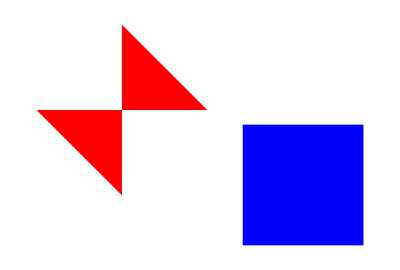

```mathematica
(* Question 4.2 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{0, Sqrt[2]},{Sqrt[2] - (1/Sqrt[2]), Sqrt[2] + (1/Sqrt[2])},{0, 2*Sqrt[2]},{(1/Sqrt[2])- Sqrt[2],(1/Sqrt[2])+ Sqrt[2]}};
MatrixForm[x]
MatrixForm[xp]
{error, f} = FindGeometricTransform[xp, x]
MatrixForm[f[x]]
Graphics[{{Blue,Polygon[x]},{Red,f[Polygon[x]]}}]
Graphics[{{Blue,Polygon[x]},{Green,Polygon[xp]}}];
```

{0.,TransformationFunction[(0. | -1. | -1.
1. | 0. | 1.
0. | 0. | 1.)]}

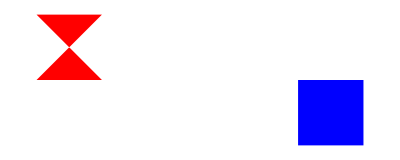

```mathematica
(* Question 4.3 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{-2,2},{-2,3},{-3,3}, {-3,2}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x]
Graphics[{{Blue,Polygon[x]},{Red,f[Polygon[x]]}}]
Graphics[{{Blue,Polygon[x]},{Green,Polygon[xp]}}];
```

{4.63127×10^-15,TransformationFunction[(3. | 1.88556×10^-15 | -4.56949×10^-15
-5.32907×10^-15 | 5. | -2.66454×10^-15
0. | 0. | 1.)]}

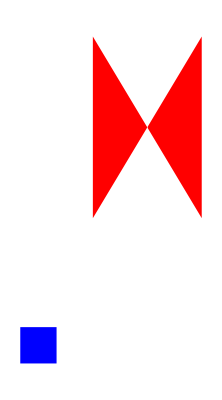

```mathematica
(* Question 4.4 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{3,5},{6,5},{6,10}, {3,10}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x]
Graphics[{{Blue,Polygon[x]},{Red,f[Polygon[x]]}}]
Graphics[{{Blue,Polygon[x]},{Green,Polygon[xp]}}];
```

(1 | 3 | 0
5 | 1 | 0
0 | 0 | 1)

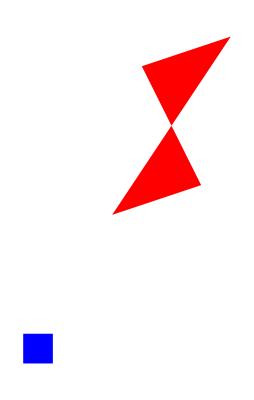

```mathematica
(* Question 4.5 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{4,6},{5,11},{8,12}, {7,7}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
MatrixForm[Round[TransformationMatrix[f]]]
Graphics[{{Blue,Polygon[x]},{Red,f[Polygon[x]]}}]
Graphics[{{Blue,Polygon[x]},{Green,Polygon[xp]}}];
```

(0 | -1 | 1
1 | 0 | 1
0 | 0 | 1)

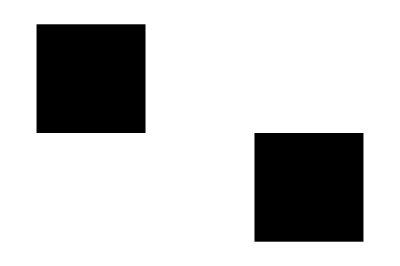

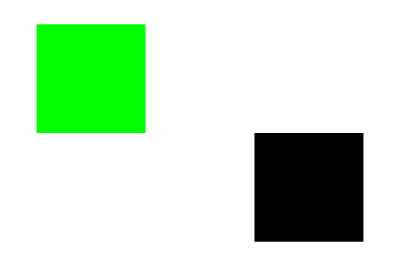

```mathematica
(* Question 4.6 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{0,2},{0,3},{-1, 3}, {-1,2}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
MatrixForm[Round[TransformationMatrix[f]]]
g = Polygon[x,VertexColors->{Red,Green,Blue, Yellow}];
Graphics[{g,GeometricTransformation[g,f]}]
Graphics[{g,{Green,Polygon[xp]}}]
```

(0 | -1 | -1
1 | 0 | 1
0 | 0 | 1)

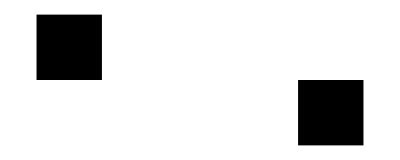

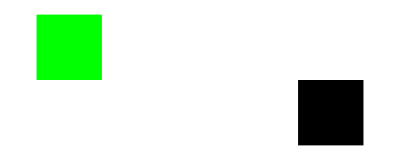

```mathematica
(* Question 4.7 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{-2,2},{-2,3},{-3,3},{-3,2}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
MatrixForm[Round[TransformationMatrix[f]]]
g = Polygon[x,VertexColors->{Red,Green,Blue, Yellow}];
Graphics[{g,GeometricTransformation[g,f]}]
Graphics[{g,{Green,Polygon[xp]}}]
```

(3 | 0 | 1
0 | 5 | 1
0 | 0 | 1)

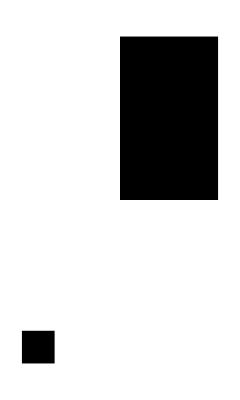

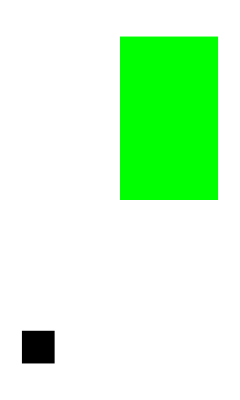

```mathematica
(* Question 4.8 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{4,6},{7,6},{7,11},{4,11}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
MatrixForm[Round[TransformationMatrix[f]]]
g = Polygon[x,VertexColors->{Red,Green,Blue, Yellow}];
Graphics[{g,GeometricTransformation[g,f]}]
Graphics[{g,{Green,Polygon[xp]}}]
```

(0 | -5 | 0
3 | 0 | 0
0 | 0 | 1)

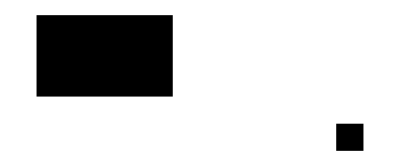

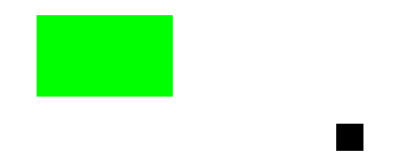

```mathematica
(* Question 4.9 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{-5,3},{-5,6},{-10,6},{-10,3}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
MatrixForm[Round[TransformationMatrix[f]]]
g = Polygon[x,VertexColors->{Red,Green,Blue, Yellow}];
Graphics[{g,GeometricTransformation[g,f]}]
Graphics[{g,{Green,Polygon[xp]}}]
```

(-5 | -1 | 0
1 | 3 | 0
0 | 0 | 1)

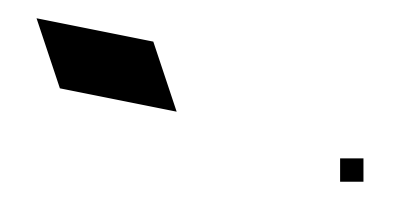

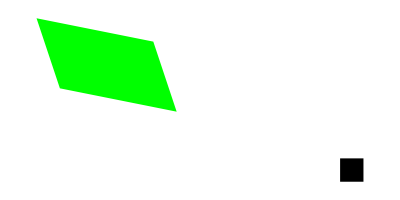

```mathematica
(* Question 4.10 *)
x = {{1,1},{2,1},{2,2},{1,2}};
xp = {{-6,4},{-11,5},{-12,8},{-7,7}};
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
MatrixForm[Round[TransformationMatrix[f]]]
g = Polygon[x,VertexColors->{Red,Green,Blue, Yellow}];
Graphics[{g,GeometricTransformation[g,f]}]
Graphics[{g,{Green,Polygon[xp]}}]
```